```mathematica
Lx=10;Ly=3;Lz=25;M=8.8*10^5;Subscript[μ, 0]=4π*10^-7;
BX[x_,y_,z_,Mx_,My_,Mz_]:=Subscript[μ, 0]*M/(4π)*Sum[(-1)^(k+l+m)*Log[(z-Mz)+(-1)^m(Lz/2)+√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2)],{k,1,2},{l,1,2},{m,1,2}];
BY[x_,y_,z_,Mx_,My_,Mz_]:=Subscript[μ, 0]*-M/(4π)*Sum[(-1)^(k+l+m)*(((y-My)+(-1)^l(Ly/2))((x-Mx)+(-1)^k(Lx/2)))/(Abs[(y-My)+(-1)^l(Ly/2)]*Abs[(x-Mx)+(-1)^k(Lx/2)])*ArcTan[(Abs[(x-Mx)+(-1)^k(Lx/2)]*((z-Mz)+(-1)^m(Lz/2)))/(Abs[(y-My)+(-1)^l(Ly/2)]*√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2))],{k,1,2},{l,1,2},{m,1,2}];
(*BY[x_,y_,z_,Mx_,My_,Mz_]:=If[Abs[y]≤Ly/2&&Abs[x]≤Lx/2&&Abs[z]≤Lz/2,-BY0[x,y,z,Mx,My,Mz],BY0[x,y,z,Mx,My,Mz]];*)
BZ[x_,y_,z_,Mx_,My_,Mz_]:=Subscript[μ, 0]*M/(4π)*Sum[(-1)^(k+l+m)*Log[(x-Mx)+(-1)^k(Lx/2)+√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2)],{k,1,2},{l,1,2},{m,1,2}];

BSX[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[BX[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BSY[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[BY[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BSZ[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[BZ[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BS[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sqrt[BSX[x,y,z,Xstack,Ystack,Zstack]^2+BSY[x,y,z,Xstack,Ystack,Zstack]^2+BSZ[x,y,z,Xstack,Ystack,Zstack]^2];
```

```mathematica
stackposition1={37,0,49};
stackposition2={37,0,-49};
stackposition3={-37,0,49};
stackposition4={-37,0,-49};
```

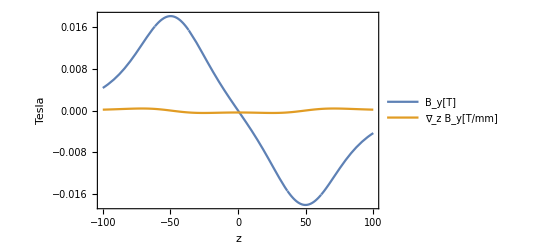

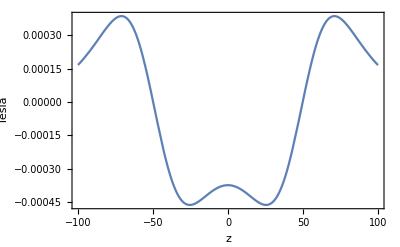

```mathematica
BYcentral[z_]:=-BSY[0,0,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,0,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,0,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,0,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
len=2000;δz=200/len;z0=-100;
dataB=Table[{z0+i*δz,BYcentral[z0+i*δz]},{i,0,len}];
(*data∇B=Table[{z0+i*δz,(BYcentral[z0+(i+1)*δz]-BYcentral[z0+i*δz])/δz},{i,0,len}];*)
BYcc=Interpolation@dataB;
(*gradient=Interpolation@data∇B;*)
Plot[{BYcc[z],BYcc'[z]},{z,-100,100},PlotLegends->{"B_y[T]","∇_z B_y[T/mm]"},Frame->True,FrameLabel->{"z","Tesla"}]
Plot[BYcc'[z],{z,-100,100},Frame->True,FrameLabel->{"z","Tesla"}]
```

```mathematica
StreamDensityPlot[{-BSY[0,y,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,y,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,y,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,y,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]],-BSZ[0,y,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]+-BSZ[0,y,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSZ[0,y,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSZ[0,y,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]]},{y,-100,100},{z,-100,100}]
```

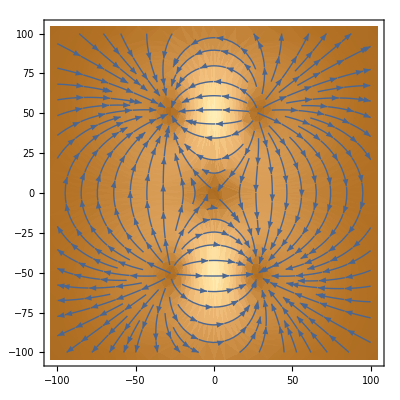

{{-100,0.00157838},{-19991/200,0.00158024},{-9991/100,0.00158211},{-19973/200,0.00158399},{-4991/50,0.00158586},{-3991/40,0.00158774},1990,{-509/50,0.00357203},{-2027/200,0.00355816},{-1009/100,0.00354427},{-2009/200,0.00353035},{-10,0.00351641}}
 |  |  |  |

0.00681302

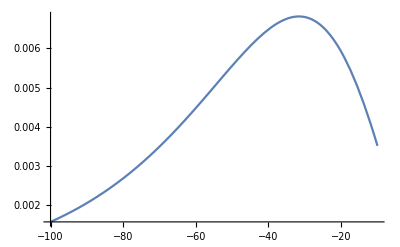

```mathematica
BYcentral[y_]:=-BSY[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
BXcentral[y_]:=-BSX[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSX[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSX[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSX[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
BZcentral[y_]:=-BSZ[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSZ[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSZ[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSZ[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
Bmagnitude[y_]:=Sqrt[BXcentral[y]^2+BYcentral[y]^2+BZcentral[y]^2];
leny=2000;δy=90/leny;y0=-100;
datamagnitude=Table[{y0+i*δy,Bmagnitude[y0+i*δy]},{i,0,leny}];
Max[datamagnitude[[All,2]]]
BMa=Interpolation@datamagnitude;
Plot[BMa[y],{y,-100,-10}]
```

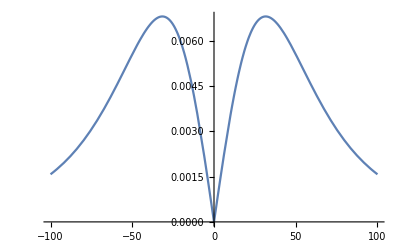

```mathematica
Plot[Bmagnitude[y],{y,-100,100}]
```

```mathematica
(*Coil magnetic field*)
μ0=4π*10^-7;n=11;current=400;a0=3.75*10^-2;b0=6.1*10^-2;c0=8.5*10^-2;L=2;
solenoid[r_,z_]:=Integrate[r^2/((r^2+(z-x)^2)^(3/2)),{x,0,L}]+Integrate[r^2/((r^2+(z+x)^2)^(3/2)),{x,0,L}];
intepart=Assuming[Element[z,Reals],Integrate[solenoid[r,z],{r,a0,c0}]];
Bsma[z_]:=(μ0*(n/L)*current)/(2(c0-a0))*intepart;
Bb[z_]:=(μ0*n*current)/2*a0^2*(1/((a0^2+(z+a0/2)^2)^(3/2))+1/((a0^2+(z-a0/2)^2)^(3/2)));
```

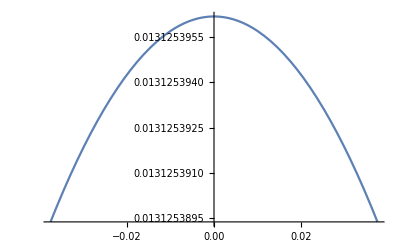

```mathematica
Plot[100*Bsma[z],{z,-a0,a0}]
```

```mathematica
Clear["Gloabl`*"]
```